#### Test circles

```mathematica
Animate[
Show[
Graphics[{
Circle[{-3,0},1],
Line[{{-3,0},{Cos[-t]-3,Sin[-t]},{0,Sin[-t]}}]

},{Axes->True,PlotRange->{-1,1}}],
Plot[Sin[x-t],{x,0,7}]
],{t,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
	Show[
		Graphics[
			{
				Circle[{-3,0},1],
				Line[{{-3,0},{Cos[-t]-3,Sin[-t]},{0,Sin[-t]}}]
			},
		{Axes->True,PlotRange->{-3,3}}],
	Plot[Sin[x-t],{x,0,7}]
	],
{t,2*Pi},AnimationRunning->False]
```

For Sin[x]+Cos[2x]

```mathematica
FourierSeries[Sin[x]+Cos[2x],x,3]//ComplexExpand
```

Cos[2 x]+Sin[x]

```mathematica
Animate[
	Show[
		Graphics[
			{
				Circle[{-3,0},1],
				Circle[{Cos[-t]-3,Sin[-t]},1],
				Line[{
				{-3,0},
				{-3,0}+{Cos[-t],Sin[-t]},
				{-3,0}+{Cos[-t],Sin[-t]}+{-Sin[-2t],Cos[-2t]},
				{0,Sin[-t]+Cos[-2t]}
				}]
			},
		{Axes->True,PlotRange->{-3,3}}],
	Plot[Sin[x-t]+Cos[2(x-t)],{x,0,7}]
	],
{t,2*Pi},AnimationRunning->False]
```

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

```mathematica
FourierCosCoefficient[Sin[x],x,5]//ComplexExpand
```

0

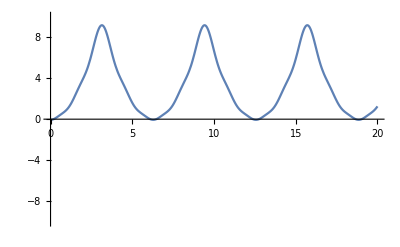

```mathematica
Plot[#1,{x,0,20},PlotRange->{-10,10}]&@Evaluate[FourierSeries[x^2,x,5]//ComplexExpand]
```

```mathematica
Animate[
	Show[
		Graphics[
			{
				Circle[{-7,0},4],
				Circle[{-4Cos[t]-7,-4Sin[t]},1],
				Circle[{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]},(4/9)],
				Circle[{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]}+{-(4/9)Cos[-3t],(-4/9)Sin[-3t]},0.25],
				Line[{
				{-7,0},
				{-7,0}+{-4Cos[t],-4Sin[t]},
				{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]},
				{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]}+{-(4/9)Cos[-3t],(-4/9)Sin[-3t]},
				{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]}+{-(4/9)Cos[-3t],(-4/9)Sin[-3t]}+{0.25Cos[-4t],0.25Sin[-4t]},
				
				{0,-4Sin[-t]+Sin[-2t]+(-4/9)Sin[-3t]+0.25Sin[-4t]}}]
				
			},
		{Axes->True,PlotRange->{-10,10}}],Plot[ -4 Cos[(x+t)]+Cos[2(x+t)]-4/9 Cos[3(x+t)]+1/4 Cos[4(x+t)]-4/25 Cos[5(x+t)],{x,0,20}]
	(*Plot[ Cos[x-t]+Cos[2 (x-t)]-4/9 Cos[3 (x-t)]+1/4 Cos[4 (x-t)]-4/25 Cos[5 (x-t)],{x,0,20}]*)
	],
{t,0,-2*Pi},AnimationRunning->False]
```

```mathematica
test2=Show[Plot[#1,{x,0,20}]&/@Apply[List,-4 Cos[(x+t)]+Cos[2(x+t)]-4/9 Cos[3(x+t)]+1/4 Cos[4(x+t)]-4/25 Cos[5(x+t)]]]
```

-Graphics-

```mathematica
?ListPlot
```

```mathematica
Animate[Graphics[circleTest,Axes->True,PlotRange->{-10,10}],{t,0,-2Pi}]
```

```mathematica
circleTest=Circle[{-7,0},#1]&/@Apply[List,4 Cos[(x+t)]+Cos[2(x+t)]+4/9 Cos[3(x+t)]+1/4 Cos[4(x+t)]+4/25 Cos[5(x+t)]]/.x+t->t
```

{Circle[{-7,0},4 Cos[t]],Circle[{-7,0},Cos[2 t]],Circle[{-7,0},4/9 Cos[3 t]],Circle[{-7,0},1/4 Cos[4 t]],Circle[{-7,0},4/25 Cos[5 t]]}

```mathematica
test=Apply[List,-4 Cos[(x+t)]+Cos[2(x+t)]-4/9 Cos[3(x+t)]+1/4 Cos[4(x+t)]-4/25 Cos[5(x+t)]];Animate[Plot[ #1,{x,0,20}],{t,0,-2Pi},AnimationRunning->False]&/@Apply[List,-4 Cos[(x+t)]+Cos[2(x+t)]-4/9 Cos[3(x+t)]+1/4 Cos[4(x+t)]-4/25 Cos[5(x+t)]]
```

```mathematica
ClearAll[fourierGraphics]

fourierGraphics[function_,variable_,numberOfCircles_]:=
Block[{
	rawFouier =Apply[List,FourierCoefficient[function,variable,numberOfCircles]],
	radii=Table[FourierCosCoefficient[function,variable,p],{p,1,numberOfCircles}],
	rawprotocoordinate,circleList,coordinateList,lineList,lastCoordinate,plotCoordinate,range
},
rawprotocoordinate=Echo@MapThread[Times,{Apply[List,radii],Cos[Range[numberOfCircles]*x]}];
coordinateList=Echo@(MapThread[List,{rawprotocoordinate,rawprotocoordinate/.Cos->Sin}]);
circleList=Echo@MapThread[Circle,{Drop[Prepend[coordinateList,{Total[radii]+2,0}],-1],Abs@radii}];
lineList=Echo@Line[Plus@@@Table[coordinateList[[;;n]],{n,1,Length[coordinateList]}]//Prepend[{0,0}]];
lastCoordinate=Echo@{0,Take[Take[lineList,-1],-1]};
plotCoordinate=Echo@Total[rawprotocoordinate/.x->(x+t)];
range=Echo@{-Total[Abs@radii],Total[Abs@radii]};
Print[radii//Length];
	Animate[
		Show[
			Graphics[
				{#1,#2,lastCoordinate},
				{Axes->True,PlotRange->{-10,10}}],
			Plot[plotCoordinate,{x,0,20}]
	
	],
{t,0,-2*Pi},AnimationRunning->False]&@Evaluate[(circleList),(lineList)]
]
```

```mathematica
Line[{
				{-7,0},
				{-7,0}+{-4Cos[t],-4Sin[t]},
				{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]},
				{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]}+{-(4/9)Cos[-3t],(-4/9)Sin[-3t]},
				{-7,0}+{-4Cos[-t],-4Sin[-t]}+{Cos[-2t],Sin[-2t]}+{-(4/9)Cos[-3t],(-4/9)Sin[-3t]}+{0.25Cos[-4t],0.25Sin[-4t]}}]
```

```mathematica
ClearAll[unblendedCircleSmoothie]

unblendedCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot
		},
		circleList=Circle[{-maxRadius,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius,basicCoord/.Cos->Sin}];
		maxRadius=Max[Abs@fourierCoeff];
		lineList=Line[{{-maxRadius,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		
		prePlot=(Transpose[{basicCoord,color}])/.variable->(variable+$time);
		plotList=Plot[#1,{x,0,10},PlotStyle->#2]&@@@(Transpose[{basicCoord,color}])/.variable->(variable+$time);

		Print[{"circleList",circleList, "styledlines", styledLines, "plotList", plotList}];
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				#3,PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->True]&@@{circleList,styledLines,plotList}
	
	
	]
```

```mathematica
Attributes[Manipulate]
```

{HoldAll,Protected,ReadProtected}

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::write: Tag ReplaceAll in … is Protected.

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

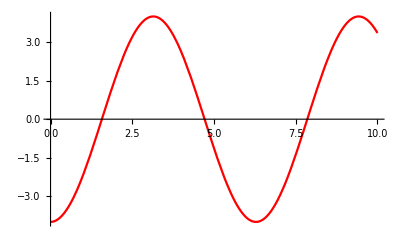
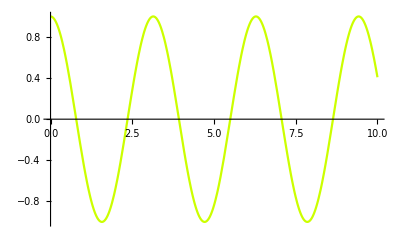
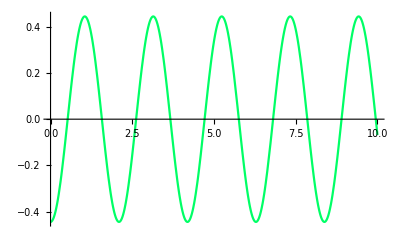
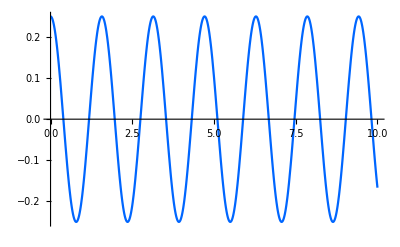
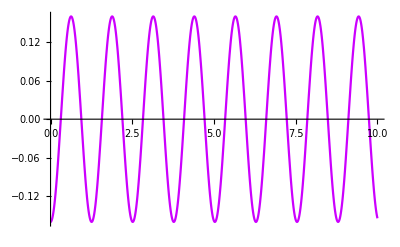
{circleList,{Circle[{-4,0},4],Circle[{-4,0},1],Circle[{-4,0},4/9],Circle[{-4,0},1/4],Circle[{-4,0},4/25]},styledlines,{Line[{{-4,0},{-4-4 Cos[$time],-4 Sin[$time]},{0,-4 Sin[$time]}}],Line[{{-4,0},{-4+Cos[2 $time],Sin[2 $time]},{0,Sin[2 $time]}}],Line[{{-4,0},{-4-4/9 Cos[3 $time],-4/9 Sin[3 $time]},{0,-4/9 Sin[3 $time]}}],Line[{{-4,0},{-4+1/4 Cos[4 $time],1/4 Sin[4 $time]},{0,1/4 Sin[4 $time]}}],Line[{{-4,0},{-4-4/25 Cos[5 $time],-4/25 Sin[5 $time]},{0,-4/25 Sin[5 $time]}}]},plotList,$time+({-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}/.x)}

```mathematica
unblendedCircleSmoothie[x^2,x,5]
```

#### Testing code (No longer in use)

```mathematica
list1={lineList,lineList2,lineList3}
```

{lineList,lineList2,lineList3}

```mathematica
list2={color,color2,color3}
```

{color,color2,color3}

```mathematica
MapThread[Style,{list1,list2}]
```

{Style[lineList,color],Style[lineList2,color2],Style[lineList3,color3]}

```mathematica
Drop[Hue[#]&/@Range[0,1,0.20],-1]
```

{Hue[0.],Hue[0.2],Hue[0.4],Hue[0.6000000000000001],Hue[0.8]}

```mathematica
radius=Table[FourierCosCoefficient[x^2,x,p],{p,1,5}]
```

{-4,1,-4/9,1/4,-4/25}

```mathematica
basicCoord=MapThread[Times,{radius,Cos[Range[5]*x]}]
```

{-4 Cos[x],Cos[2 x],-4/9 Cos[3 x],1/4 Cos[4 x],-4/25 Cos[5 x]}

```mathematica
Transpose[{basicCoord-7,basicCoord/.Cos->Sin}]
```

{{-7-4 Cos[x],-4 Sin[x]},{-7+Cos[2 x],Sin[2 x]},{-7-4/9 Cos[3 x],-4/9 Sin[3 x]},{-7+1/4 Cos[4 x],1/4 Sin[4 x]},{-7-4/25 Cos[5 x],-4/25 Sin[5 x]}}

```mathematica
Style[Line[{{-maxRadius,0},#1,{0,#1[[2]]}}],Color]&/@basicCoord
```

{Style[Line[{{-7,0},-4 Cos[x],{0,YCoord}}],Color],Style[Line[{{-7,0},Cos[2 x],{0,YCoord}}],Color],Style[Line[{{-7,0},-4/9 Cos[3 x],{0,YCoord}}],Color],Style[Line[{{-7,0},1/4 Cos[4 x],{0,YCoord}}],Color],Style[Line[{{-7,0},-4/25 Cos[5 x],{0,YCoord}}],Color]}

```mathematica
circleTest2=Circle[{-7,0},#1]&/@Abs@Table[FourierCosCoefficient[x^2,x,p],{p,1,5}];
	Animate[
		Show[
			Graphics[{#1,
				Style[Line[{{-7,0},{-4Cos[t]-7,-4Sin[t]},{0,-4Sin[t]}}],Red],
				Style[Line[{{-7,0},{Cos[-2t]-7,Sin[-2t]},{0,Sin[-2t]}}],Green],
				Style[Line[{{-7,0},{-(4/9)Cos[-3t]-7,(-4/9)Sin[-3t]},{0,(-4/9)Sin[-3t]}}],Blue]}
			,Axes->True],
			{
			Plot[-4Cos[x+t-(Pi/2)],{x,0,10},PlotStyle->Red],
			Plot[Cos[-2(x+t-(3Pi/4))],{x,0,10},PlotStyle->Green],
			Plot[-(4/9)Cos[-3(x+t-(Pi/2))],{x,0,10},PlotStyle->Blue]
			
			}
			
	],{t,0,-2Pi},AnimationRunning->False]&@circleTest2
```

```mathematica
circleTest2=Circle[{-7,0},#1]&/@Abs@Table[FourierCosCoefficient[x^2,x,p],{p,1,5}]
Animate[Graphics[#1,Axes->True],{t,0,-2Pi}]&@circleTest2
```

{Circle[{-7,0},4],Circle[{-7,0},1],Circle[{-7,0},4/9],Circle[{-7,0},1/4],Circle[{-7,0},4/25]}

```mathematica
fourierGraphics[x^2,x,5]
```

{-4 Cos[x],Cos[2 x],-4/9 Cos[3 x],1/4 Cos[4 x],-4/25 Cos[5 x]}

{{-4 Cos[x],-4 Sin[x]},{Cos[2 x],Sin[2 x]},{-4/9 Cos[3 x],-4/9 Sin[3 x]},{1/4 Cos[4 x],1/4 Sin[4 x]},{-4/25 Cos[5 x],-4/25 Sin[5 x]}}

{Circle[{-1219/900,0},4],Circle[{-4 Cos[x],-4 Sin[x]},1],Circle[{Cos[2 x],Sin[2 x]},4/9],Circle[{-4/9 Cos[3 x],-4/9 Sin[3 x]},1/4],Circle[{1/4 Cos[4 x],1/4 Sin[4 x]},4/25]}

Line[{{0,0},{-4 Cos[x],-4 Sin[x]},{-4 Cos[x]+Cos[2 x],-4 Sin[x]+Sin[2 x]},{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]},{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]},{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]-4/25 Sin[5 x]}}]

{0,Line[{{0,0},{-4 Cos[x],-4 Sin[x]},{-4 Cos[x]+Cos[2 x],-4 Sin[x]+Sin[2 x]},{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]},{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]},{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]-4/25 Sin[5 x]}}]}

-4 Cos[t+x]+Cos[2 (t+x)]-4/9 Cos[3 (t+x)]+1/4 Cos[4 (t+x)]-4/25 Cos[5 (t+x)]

{-5269/900,5269/900}

5

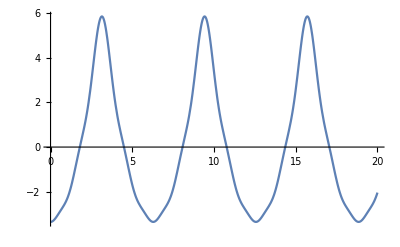

```mathematica
Plot[rawcoordinate,{x,0,20}]
```

```mathematica
(MapThread[List,{rawcoordinate,rawcoordinate/.Cos->Sin}])
```

{{(24/π-6 π) Cos[t],-(24/π-6 π) Sin[t]},{3/2 π Cos[2 t],-3/2 π Sin[2 t]},{(8/(27 π)-(2 π)/3) Cos[3 t],-(8/(27 π)-(2 π)/3) Sin[3 t]},{3/8 π Cos[4 t],-3/8 π Sin[4 t]},{(6 (4-25 π^2) Cos[5 t])/(625 π),-(6 (4-25 π^2) Sin[5 t])/(625 π)}}

```mathematica
Cos[Range[5]*x]
```

{Cos[x],Cos[2 x],Cos[3 x],Cos[4 x],Cos[5 x]}

```mathematica
Animate[
Show[
Graphics[{
Circle[{0,0},0.5],
Circle[{0.5Cos[-t],0.5Sin[-t]},0.5],

Line[{{0,0},{0.5Cos[-t],0.5Sin[-t]}}],
Line[{{0.5Cos[-t],0.5Sin[-t]},{0.5Cos[-t]-0.5Cos[t],0.5Sin[-t]-0.5Sin[t]}}],
},{Axes->True,PlotRange->{-1,1}}],
Plot[Sin[x-t],{x,0,7}]
],{t,2*Pi},AnimationRunning->False]
```